# ImStat

Statistics of image collection

## Setup and data collection

## Config

Source folder for JPG files:

```mathematica
imageDir="/media/superraid/images/images/";
```

Nr of raw files:

```mathematica
rawFileNames=FileNames["*.CR2",imageDir,∞];
```

```mathematica
nrRawFiles=rawFileNames//Length
```

16483

```mathematica
jpgFileNames=FileNames["*.jpg"|"*.JPG",imageDir,∞];
```

Number of images found:

```mathematica
nrJpgFiles=Length[jpgFileNames]
```

5389

Folder for local data storage:

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"dataStorage"}]
```

/home/malte/Dev/imStat/dataStorage

```mathematica
CreateDirectory[dataDir]
```

/home/malte/Dev/imStat/dataStorage

## Retrieve mini JPG files and basic data

Compute data file name from original path, making sure that no collisions will occur:

```mathematica
(Union[Hash[#,"CRC32"]&/@jpgFileNames]//Length)==nrJpgFiles
```

True

```mathematica
storageFile[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".dst"}];
```

```mathematica
storageFileImg[path_]:=storageFileImg[path]=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".jpg"}];
```

Fetch original image and save data into data file:

```mathematica
createData[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createData[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model,exifData},
exifData=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","Date","Exposure","FocalLength","ImageSize","ISOSpeed","Manufacturer","Model"}}];
If[!MatchQ[exifData,{_,_,_,_DateObject,_,_,{_,_},_,_String,_String}],
Return[$Failed];
];
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300},Resampling->"Bilinear"];
Put[{dimensions,exifData},storageFile[path]];
Export[storageFileImg[path],smallImg];
]
```

```mathematica
ClearAll[createDataRaw]
```

```mathematica
createDataRaw[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createDataRaw[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model,exifData,cleanExif},
exifData=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","Date","ExposureTime","FocalLength","ImageSize","ISOSpeedRatings","Make","Model"}}];
If[!MatchQ[exifData,{_,_,_,_DateObject,_,_,{_,_},_,_String,_String}],
Return[$Failed];
];
cleanExif=exifData;
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300},Resampling->"Bilinear"];
Put[{dimensions,cleanExif},storageFile[path]];
Quiet@Export[storageFileImg[path],smallImg];
]
```

File size:

```mathematica
fileSizes={#,FileByteCount[#]}&/@Join[jpgFileNames,rawFileNames];
```

```mathematica
Put[fileSizes,FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Retrieving file sizes:

```mathematica
fileSizes=Get[FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Fetch data in order of preference {memory, data file}:

```mathematica
ClearAll[getData];
getData[path_]/;FileExistsQ[storageFile[path]]:=getData[path]={Import[storageFileImg[path]],Get[storageFile[path]]}
```

```mathematica
getData[_]:=$Failed
```

Accessor functions for properties:

```mathematica
getData[path_,"Date"]:=getData[path][[2,2,4]]
```

```mathematica
getData[path_,"Orientation"]:=getData[path][[2,2,3]]
```

```mathematica
getData[path_,"Camera"]:=getData[path][[2,2,9;;10]]
```

```mathematica
getData[path_,"Aperture"]:=getData[path][[2,2,1]]
```

```mathematica
getData[path_,"BitDepth"]:=getData[path][[2,2,2]]
```

```mathematica
getData[path_,"Exposure"]:=getData[path][[2,2,5]]
```

```mathematica
getData[path_,"FocalLength"]:=getData[path][[2,2,6]]
```

```mathematica
getData[path_,"ImageSize"]:=getData[path][[2,1]]
```

```mathematica
getData[path_,"ISO"]:=getData[path][[2,2,8]]
```

## Retrieve image data

### JPG

```mathematica
Monitor[
ParallelDo[createData[jpgFileNames[[i]]],{i,Length[jpgFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir],{0,2Length[jpgFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

Import::noelem: The Import element ""Aperture"" is not present when importing as "JPEG".

Import::noelem: The Import element ""CameraTopOrientation"" is not present when importing as "JPEG".

Import::noelem: The Import element ""Date"" is not present when importing as "JPEG".

General::stop: Further output of Import :: noelem will be suppressed during this calculation.

Import::noelem: The Import element ""Aperture"" is not present when importing as "JPEG".

Import::noelem: The Import element ""CameraTopOrientation"" is not present when importing as "JPEG".

Import::noelem: The Import element ""Date"" is not present when importing as "JPEG".

General::stop: Further output of Import :: noelem will be suppressed during this calculation.

Import::noelem: The Import element ""Aperture"" is not present when importing as "JPEG".

Import::noelem: The Import element ""CameraTopOrientation"" is not present when importing as "JPEG".

Import::noelem: The Import element ""Date"" is not present when importing as "JPEG".

Import::noelem: The Import element ""Aperture"" is not present when importing as "JPEG".

General::stop: Further output of Import :: noelem will be suppressed during this calculation.

Import::noelem: The Import element ""CameraTopOrientation"" is not present when importing as "JPEG".

Import::noelem: The Import element ""Date"" is not present when importing as "JPEG".

General::stop: Further output of Import :: noelem will be suppressed during this calculation.

### RAW

```mathematica
Monitor[
ParallelDo[createDataRaw[rawFileNames[[i]]],{i,Length[rawFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir]-2*Length[jpgFileNames],{0,2Length[rawFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

ImageDimensions::imginv: Expecting an image or graphics instead of $Failed.

ImageResize::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of $Failed.

ImageResize::imginv: Expecting an image or graphics instead of $Failed.

### Gathering

```mathematica
goodFileNames=Select[jpgFileNames,FileExistsQ[storageFile[#]]&&FileExistsQ[storageFileImg[#]]&];
```

```mathematica
goodFileNames=Join[goodFileNames,Select[rawFileNames,FileExistsQ[storageFile[#]]&&FileExistsQ[storageFileImg[#]]&]];
```

## Results

## Number of images taken

```mathematica
nrJpg=Length[jpgFileNames]
```

5389

```mathematica
nrRaw=Length[rawFileNames]
```

16483

```mathematica
nrGood=Length[goodFileNames]
```

21835

```mathematica
nrNotGood=nrJpg+nrRaw-nrGood
```

37

```mathematica
PieChart[{nrGood,nrNotGood},ChartLabels->{"","No data"}]
```

-Graphics-

## Images taken over time

```mathematica
imageDates=Monitor[
Table[getData[goodFileNames[[i]],"Date"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

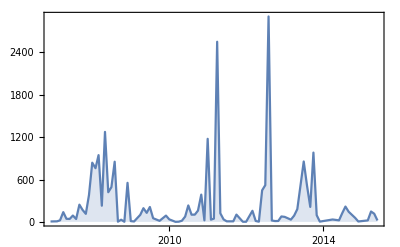

```mathematica
timeTakenPlot=DateListPlot[Tally@Map[#[{"Year","Month"}]&,imageDates],Joined->True,PlotRange->All,Filling->Axis,GridLines->None]
```

## Camera models

```mathematica
imageCameras=Monitor[
Table[getData[goodFileNames[[i]],"Camera"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
imageCameras=Replace[imageCameras,{{"Canon","EOS 40D"}->{"Canon","Canon EOS 40D"},{"Canon","EOS 350D"}->{"Canon","Canon EOS Kiss Digital N"},{"Canon","EOS 650D"}->{"Canon","Canon EOS 650D"}},{1}];
```

```mathematica
cameralist1=Sort[Tally@imageCameras,#1[[2]]>#2[[2]]&]
```

{{{Canon,Canon EOS Kiss Digital N},12101},{{Canon,Canon EOS 650D},7888},{{Sony Ericsson,K800i},1074},{{NIKON CORPORATION,NIKON D3000},448},{{Canon,Canon EOS 40D},250},{{HTC,HTC Hero},21},{{CASIO COMPUTER CO.,LTD.,EX-H15     },16},{{google,Nexus S},14},{{CASIO COMPUTER CO.,LTD.,EX-Z100    },12},{{CASIO COMPUTER CO.,LTD.,EX-G1      },5},{{HTC,HTC Desire},4},{{Sony Ericsson,W890i},2}}

```mathematica
cameraBreakPoint=20;
```

```mathematica
{cameraLabel,cameraData}=Transpose@Append[Select[cameralist1,#[[2]]≥cameraBreakPoint&],{"Other",Total[Select[cameralist1,#[[2]]<cameraBreakPoint&][[All,2]]]}]
```

{{{Canon,Canon EOS Kiss Digital N},{Canon,Canon EOS 650D},{Sony Ericsson,K800i},{NIKON CORPORATION,NIKON D3000},{Canon,Canon EOS 40D},{HTC,HTC Hero},Other},{12101,7888,1074,448,250,21,53}}

```mathematica
formatLabel[{"Canon","Canon EOS Kiss Digital N"}]="Canon 350D";
formatLabel[{"Sony Ericsson","K800i"}]="Sony Ericsson K800i";
formatLabel[{"Canon","Canon EOS 40D"}]="Canon 40D";
formatLabel[{"NIKON CORPORATION","NIKON D3000"}]="Nikon D3000";
formatLabel[{"Canon","Canon EOS 650D"}]="Canon 650D";
formatLabel[{"HTC","HTC Hero"}]:="HTC Hero";
formatLabel[{"CASIO COMPUTER CO.,LTD.","EX-G1      "}]:="Casio G1";
formatLabel[{"google","Nexus S"}]:="Nexus S";
formatLabel[{"CASIO COMPUTER CO.,LTD.","EX-Z100    "}]:="Casio Z100";
formatLabel[{"CASIO COMPUTER CO.,LTD.","EX-H15     "}]:="Casio H15";
formatLabel[{"Sony Ericsson","W890i"}]:="Sony Ericsson W890i";
formatLabel[{"HTC","HTC Desire"}]:="HTC Desire";
formatLabel["Other"]:="Other";
```

```mathematica
formatLabel/@cameraLabel
```

{Canon 350D,Canon 650D,Sony Ericsson K800i,Nikon D3000,Canon 40D,HTC Hero,Other}

```mathematica
cameraPie=PieChart[cameraData,ChartLegends->formatLabel/@cameraLabel]
```

-Graphics-

```mathematica
gatheredData=GatherBy[getData/@goodFileNames,#[[2,2,-1]]&];
```

```mathematica
gatheredAbsoluteData=(AbsoluteTime/@#[[All,2,2,4]])&/@gatheredData;
```

```mathematica
gatheredCameras=((#[[All,2,2,-2;;-1]])&/@gatheredData)[[All,1]];
```

```mathematica
cameraMinMaxTimes={Min[#],Max[#]}&/@gatheredAbsoluteData
```

{{3407418896,3549444936},{3374342953,3424212073},{3448542854,3543403300},{3489483327,3543405998},{3549721924,3643195007},{3493891390,3500556243},{3506510380,3506514446},{3456513930,3477330971},{3505570682,3536257160},{3493259701,3499281425},{3495543634,3496600315},{3498653196,3499155668},{3407424677,3549445016},{3438935575,3543403300},{3549722463,3643195026}}

```mathematica
cleanMinMaxTimes=Sort[Select[Transpose[{gatheredCameras,cameraMinMaxTimes}],MemberQ[cameraLabel,#[[1]]]&],#1[[2,1]]>#2[[2,1]]&]
```

{{{Canon,Canon EOS 650D},{3549721924,3643195007}},{{HTC,HTC Hero},{3493891390,3500556243}},{{NIKON CORPORATION,NIKON D3000},{3489483327,3543405998}},{{Canon,Canon EOS 40D},{3448542854,3543403300}},{{Canon,Canon EOS Kiss Digital N},{3407418896,3549444936}},{{Sony Ericsson,K800i},{3374342953,3424212073}}}

```mathematica
minCameraTime=Min[cleanMinMaxTimes[[All,2]]]
```

3374342953

```mathematica
maxCameraTime=Max[cleanMinMaxTimes[[All,2]]]
```

3643195007

```mathematica
yearTickFn[min_,max_]:=Table[{i,DateList[i+minCameraTime][[1]]},{i,min,max,3 10^7}]
```

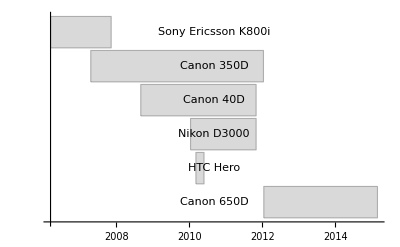

```mathematica
cameraBar=BarChart[{#[[1]]-minCameraTime,#[[2]]-#[[1]],maxCameraTime-#[[2]]}&/@cleanMinMaxTimes[[All,2]],ChartLayout->"Stacked",ChartStyle->{Directive[Transparent,EdgeForm[None]],Directive[LightGray,EdgeForm[Gray]],Directive[Transparent,EdgeForm[None]]},BarOrigin->Left,Axes->{False,True},ChartLabels->{None,Placed[formatLabel/@cleanMinMaxTimes[[All,1]],Center],None},Ticks->{yearTickFn,None}]
```

## Aperture

```mathematica
imageAperture=Monitor[
Table[getData[goodFileNames[[i]],"Aperture"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

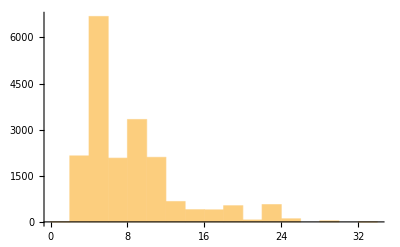

```mathematica
Histogram[imageAperture]
```

```mathematica
Manipulate[Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+2Pi/6],Sin[t+2Pi/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+2Pi/6,t,-0.1}]}],{t,0,2Pi,2Pi/6}]},ImageSize->400],{d,1,10},{o,0,2Pi}]
```

```mathematica
closedAperture=With[{d=4.27,o=0.819513},Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+(2 π)/6],Sin[t+(2 π)/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+(2 π)/6,t,-0.1}]}],{t,0,2 π,(2 π)/6}]},ImageSize->60]]
```

-Graphics-

```mathematica
openAperture=With[{d=1.12,o=0.160796},Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+(2 π)/6],Sin[t+(2 π)/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+(2 π)/6,t,-0.1}]}],{t,0,2 π,(2 π)/6}]},ImageSize->60]]
```

-Graphics-

```mathematica
apertureChart=SmoothHistogram[Replace[imageAperture,None:>Sequence[],{1}],AxesOrigin->{0,0},Axes->{True,False},PlotRangePadding->{{0,1},Automatic},PlotRange->{{-3.5,Automatic},All},Filling->Axis,Epilog->{Inset[openAperture,{-0.5,Center}],Inset[closedAperture,{25,Center}]}]
```

-Graphics-

## Time of day taken

```mathematica
timeOfDayTicks[min_,max_]:=Join[Table[{i,Round[i/60/60],{0,.01}},{i,Ceiling[min],Floor[max],60*60*2}]]
```

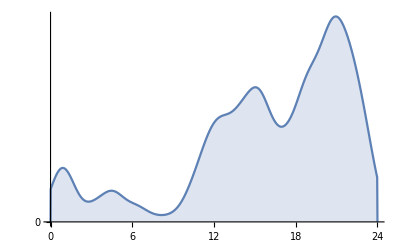

```mathematica
timeOfDayChart=SmoothHistogram[Map[Total[{60*60,60,1}*#[{"Hour","Minute","Second"}]]&,imageDates],Axes->{True,False},Filling->Axis,Ticks->timeOfDayTicks,PlotRange->{{0,24*60*60},Automatic}]
```

## Exposure

```mathematica
getData[goodFileNames[[1]],"Exposure"]
```

1/60

```mathematica
imageExposure=Monitor[
Cases[Table[getData[goodFileNames[[i]],"Exposure"],{i,Length[goodFileNames]}],Except[None|-1]],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

ImageDimensions::imginv: Expecting an image or graphics instead of $Failed.

```mathematica
totalExposure=Total[imageExposure]/60
```

459.439

```mathematica
Max[imageExposure]
```

1054.

```mathematica
Min[imageExposure]
```

1/6400

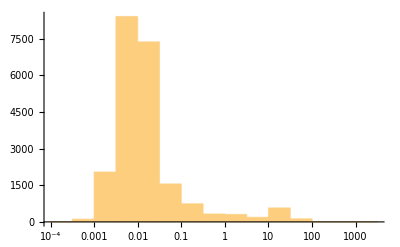

```mathematica
Histogram[imageExposure,"Log",Axes->{True,False}]
```

```mathematica
fastClock=Graphics[{EdgeForm[LightGray],Gray,Circle[],Table[Line[{{Cos[t],Sin[t]},{Cos[t],Sin[t]}/1.1}],{t,0,2Pi,2Pi/12}],FaceForm[RGBColor[0.5000076295109483,0.7750362401770047,1.]],Disk[{0,0},1,{2 2π/12,π/2}]},ImageSize->70]
```

-Graphics-

```mathematica
slowClock=Graphics[{EdgeForm[LightGray],Gray,Circle[],FaceForm[RGBColor[0.5000076295109483,0.7750362401770047,1.]],Disk[{0,0},1,{-8 2π/12,π/2}],Table[Line[{{Cos[t],Sin[t]},{Cos[t],Sin[t]}/1.1}],{t,0,2Pi,2Pi/12}]},ImageSize->70]
```

-Graphics-

```mathematica
exposureChart=SmoothHistogram[Log@imageExposure,Ticks->{Charting`ScaledTicks[{Log,Exp}],Automatic},Axes->{True,False},Filling->Axis,PlotRangePadding->{{4,Automatic},Automatic},Epilog->{Inset[fastClock,{-10,Center}],Inset[slowClock,{2,Center}]},PlotRange->All]
```

-Graphics-

## Focal length

```mathematica
imageFocalLength=Monitor[
Cases[Table[getData[goodFileNames[[i]],"FocalLength"],{i,Length[goodFileNames]}],Except[None]],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Max[imageFocalLength]
```

300.

```mathematica
Min[imageFocalLength]
```

3.43

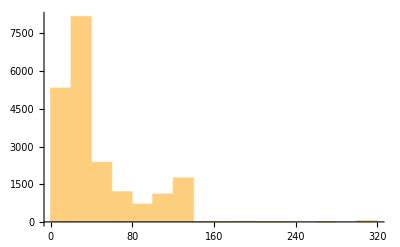

```mathematica
Histogram[imageFocalLength,Axes->{True,False}]
```

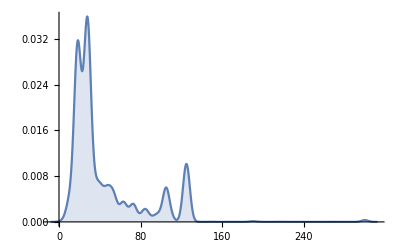

```mathematica
focalChart=SmoothHistogram[imageFocalLength,Axes->{True,False},Filling->Axis,PlotRange->All]
```

## Image size

```mathematica
imageSizes=Monitor[
Select[Table[getData[goodFileNames[[i]],"ImageSize"],{i,Length[goodFileNames]}],FreeQ[#,$Failed]&],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
talliedImageSizes=Tally[imageSizes];
```

```mathematica
miniTalliesImageSizes=Cases[talliedImageSizes,{{_,_},a_}/;a>1]
```

{{{2304,3456},677},{{3456,2304},1048},{{2630,1899},3},{{2913,2105},3},{{2704,2024},3},{{2556,1906},3},{{2393,1621},3},{{2987,2108},3},{{2883,1988},3},{{2742,2100},3},{{3102,2273},3},{{1207,1931},3},{{1960,3353},3},{{1215,1506},9},{{1506,1215},2},{{2132,3399},3},{{2147,3364},3},{{2029,3253},3},{{2921,2047},3},{{3020,2108},3},{{3131,1746},2},{{2944,1847},2},{{1689,2261},2},{{2304,1600},2},{{2736,1615},2},{{2241,3362},2},{{2064,3096},2},{{2730,1820},2},{{2215,1477},2},{{2175,1450},2},{{200,200},2},{{2012,1341},2},{{2055,3083},2},{{2021,3031},2},{{1695,2542},2},{{1449,2174},2},{{1536,2304},9},{{2089,3134},4},{{1901,2851},3},{{2547,1698},3},{{2812,1874},2},{{2604,1736},2},{{2770,1847},3},{{3036,2024},2},{{2740,1827},2},{{2817,1878},4},{{3242,2161},2},{{2128,3193},2},{{2380,1587},2},{{1826,2739},2},{{3018,2012},2},{{2882,1922},2},{{2515,1677},2},{{3123,2082},2},{{2507,1671},3},{{1947,2920},2},{{3401,2267},2},{{1883,2825},2},{{3166,2111},2},{{2746,1831},3},{{3374,2249},2},{{2137,1424},2},{{1511,1007},2},{{2483,1656},2},{{3200,2133},2},{{1783,2674},2},{{2048,1536},788},{{2304,1536},2},{{3262,2175},4},{{3304,2202},2},{{2224,3336},2},{{1399,2099},4},{{2198,3297},2},{{2581,1721},2},{{2016,3025},2},{{3280,2186},2},{{1024,683},575},{{1876,2814},2},{{2367,1578},2},{{1680,1120},2},{{2270,1513},3},{{3474,2314},9168},{{1861,2791},3},{{2084,3126},4},{{1411,2117},3},{{3311,2208},4},{{1677,2515},3},{{1280,1920},2},{{3256,2171},2},{{2820,1880},2},{{3273,2182},3},{{2077,3115},2},{{3309,2206},2},{{2249,3374},2},{{2093,3140},2},{{1716,2574},2},{{3872,2592},331},{{2592,3872},98},{{1882,2822},2},{{3143,2096},2},{{5184,3456},428},{{3456,5184},138},{{4297,2864},2},{{3297,2198},2},{{2985,4477},4},{{5035,3357},3},{{2205,3307},3},{{2786,4179},3},{{2143,3215},3},{{4388,2925},3},{{4925,3283},3},{{3762,2508},4},{{3676,2451},3},{{2938,4406},3},{{2778,4167},3},{{3385,2257},3},{{2950,4424},3},{{5089,3392},3},{{4480,2987},3},{{4941,3294},4},{{4876,3251},3},{{5001,3334},3},{{1290,1935},3},{{4913,3275},3},{{2297,1531},3},{{1937,1291},4},{{4959,3307},3},{{3524,2349},2},{{2457,1638},3},{{3247,4871},2},{{3054,2036},2},{{3070,2046},2},{{1442,2163},2},{{4612,3075},2},{{2207,3310},2},{{3084,2056},2},{{2944,4417},2},{{3330,4995},2},{{3191,4787},2},{{4873,3249},2},{{3033,4549},3},{{4549,3033},2},{{3731,2487},2},{{2658,1772},2},{{2672,1781},2},{{2532,1688},2},{{4962,3309},2},{{5057,3370},2},{{5014,3343},2},{{3388,5082},2},{{5141,3428},2},{{5103,3402},2},{{4677,3118},2},{{5055,3370},2},{{1728,2592},17},{{480,360},5},{{2314,3474},21},{{2560,1920},6},{{1920,2560},8},{{3072,2304},6},{{2304,3072},5},{{3424,2292},2},{{2816,2112},12},{{2112,2816},4},{{1552,2592},4},{{2592,1728},4},{{5204,3472},24},{{5008,3338},2},{{4372,2914},2},{{5146,3431},2},{{4136,2757},2},{{3472,5204},2},{{1536,2048},285},{{3908,2602},177},{{2602,3908},69},{{5208,3476},5659},{{3476,5208},1409}}

```mathematica
maxImgSizeNr=Max[talliedImageSizes[[All,2]]]
```

9168

```mathematica
Sort[miniTalliesImageSizes,#1[[2]]>#2[[2]]&]
```

{{{3474,2314},9168},{{5208,3476},5659},{{3476,5208},1409},{{3456,2304},1048},{{2048,1536},788},{{2304,3456},677},{{1024,683},575},{{5184,3456},428},{{3872,2592},331},{{1536,2048},285},{{3908,2602},177},{{3456,5184},138},{{2592,3872},98},{{2602,3908},69},{{5204,3472},24},{{2314,3474},21},{{1728,2592},17},{{2816,2112},12},{{1536,2304},9},{{1215,1506},9},{{1920,2560},8},{{3072,2304},6},{{2560,1920},6},{{2304,3072},5},{{480,360},5},{{2592,1728},4},{{1552,2592},4},{{2112,2816},4},{{1937,1291},4},{{4941,3294},4},{{3762,2508},4},{{2985,4477},4},{{3311,2208},4},{{2084,3126},4},{{1399,2099},4},{{3262,2175},4},{{2817,1878},4},{{2089,3134},4},{{3033,4549},3},{{2457,1638},3},{{4959,3307},3},{{2297,1531},3},{{4913,3275},3},{{1290,1935},3},{{5001,3334},3},{{4876,3251},3},{{4480,2987},3},{{5089,3392},3},{{2950,4424},3},{{3385,2257},3},{{2778,4167},3},{{2938,4406},3},{{3676,2451},3},{{4925,3283},3},{{4388,2925},3},{{2143,3215},3},{{2786,4179},3},{{2205,3307},3},{{5035,3357},3},{{3273,2182},3},{{1677,2515},3},{{1411,2117},3},{{1861,2791},3},{{2270,1513},3},{{2746,1831},3},{{2507,1671},3},{{2770,1847},3},{{2547,1698},3},{{1901,2851},3},{{3020,2108},3},{{2921,2047},3},{{2029,3253},3},{{2147,3364},3},{{2132,3399},3},{{1960,3353},3},{{1207,1931},3},{{3102,2273},3},{{2742,2100},3},{{2883,1988},3},{{2987,2108},3},{{2393,1621},3},{{2556,1906},3},{{2704,2024},3},{{2913,2105},3},{{2630,1899},3},{{3472,5204},2},{{4136,2757},2},{{5146,3431},2},{{4372,2914},2},{{5008,3338},2},{{3424,2292},2},{{5055,3370},2},{{4677,3118},2},{{5103,3402},2},{{5141,3428},2},{{3388,5082},2},{{5014,3343},2},{{5057,3370},2},{{4962,3309},2},{{2532,1688},2},{{2672,1781},2},{{2658,1772},2},{{3731,2487},2},{{4549,3033},2},{{4873,3249},2},{{3191,4787},2},{{3330,4995},2},{{2944,4417},2},{{3084,2056},2},{{2207,3310},2},{{4612,3075},2},{{1442,2163},2},{{3070,2046},2},{{3054,2036},2},{{3247,4871},2},{{3524,2349},2},{{3297,2198},2},{{4297,2864},2},{{3143,2096},2},{{1882,2822},2},{{1716,2574},2},{{2093,3140},2},{{2249,3374},2},{{3309,2206},2},{{2077,3115},2},{{2820,1880},2},{{3256,2171},2},{{1280,1920},2},{{1680,1120},2},{{2367,1578},2},{{1876,2814},2},{{3280,2186},2},{{2016,3025},2},{{2581,1721},2},{{2198,3297},2},{{2224,3336},2},{{3304,2202},2},{{2304,1536},2},{{1783,2674},2},{{3200,2133},2},{{2483,1656},2},{{1511,1007},2},{{2137,1424},2},{{3374,2249},2},{{3166,2111},2},{{1883,2825},2},{{3401,2267},2},{{1947,2920},2},{{3123,2082},2},{{2515,1677},2},{{2882,1922},2},{{3018,2012},2},{{1826,2739},2},{{2380,1587},2},{{2128,3193},2},{{3242,2161},2},{{2740,1827},2},{{3036,2024},2},{{2604,1736},2},{{2812,1874},2},{{1449,2174},2},{{1695,2542},2},{{2021,3031},2},{{2055,3083},2},{{2012,1341},2},{{200,200},2},{{2175,1450},2},{{2215,1477},2},{{2730,1820},2},{{2064,3096},2},{{2241,3362},2},{{2736,1615},2},{{2304,1600},2},{{1689,2261},2},{{2944,1847},2},{{3131,1746},2},{{1506,1215},2}}

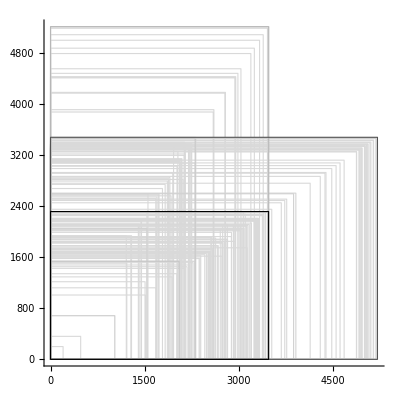

```mathematica
sizeGraphic=Graphics[{FaceForm[None],EdgeForm[Darker[LightGray,(#[[2]]/maxImgSizeNr)]],Rectangle[{0,0},#[[1]]]}&/@Sort[miniTalliesImageSizes,#1[[2]]<#2[[2]]&],Axes->True,AxesStyle->Gray,AspectRatio->1]
```

Average mexapixel

```mathematica
Select[imageSizes,!FreeQ[#,$Failed]&]
```

{}

```mathematica
mpAvg=Mean@N[Times@@@imageSizes/1000000]
```

11.1387

```mathematica
{mpMax,mpMin}={Max[#],Min[#]}&@N[Times@@@imageSizes/1000000]
```

{25.8974,0.04}

Megapixel distribution

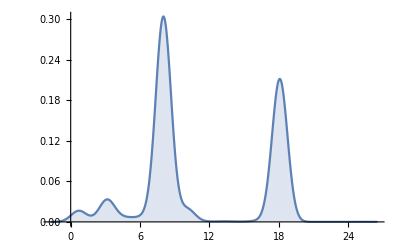

```mathematica
megaPixelChart=SmoothHistogram[Times@@@imageSizes/1000000,Axes->{True,False},Filling->Axis,PlotRange->All]
```

## ISO

```mathematica
imageISO=Monitor[
Table[getData[goodFileNames[[i]],"ISO"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{labelISO,nrISO}=HistogramList[imageISO,{100}]
```

{{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000,4100,4200,4300,4400,4500,4600,4700,4800,4900,5000,5100,5200,5300,5400,5500,5600,5700,5800,5900,6000,6100,6200,6300,6400,6500,6600,6700,6800,6900,7000,7100,7200,7300,7400,7500,7600,7700,7800,7900,8000,8100,8200,8300,8400,8500,8600,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700,9800,9900,10000,10100,10200,10300,10400,10500,10600,10700,10800,10900,11000,11100,11200,11300,11400,11500,11600,11700,11800,11900,12000,12100,12200,12300,12400,12500,12600,12700,12800,12900},{395,13192,2130,8,3537,24,52,1,808,0,17,0,0,0,0,0,1530,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,58,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47}}

```mathematica
isoChart=PieChart[nrISO,ChartLabels->Placed[labelISO,"RadialCallout"],ChartStyle->Prepend[Table[GrayLevel[1-Sqrt[i/Length[labelISO]]],{i,Length[labelISO]}],Directive[EdgeForm[Dashed],White]]]
```

-Graphics-

## Orientations

```mathematica
{orientLabel,orientNr}=Transpose@Tally[If[#[[1]]>#[[2]],"Landscape","Portrait"]&/@imageSizes]
```

{{Portrait,Landscape},{3080,18753}}

```mathematica
orientationChart=PieChart[orientNr,ChartLabels->Placed[orientLabel/.{"Landscape"->Graphics[{Gray,EdgeForm[Black],Rectangle[{0,0},{3456,2304}]},ImageSize->{30}],"Portrait"->Graphics[{Gray,EdgeForm[Black],Rectangle[{0,0},{2304,3456}]},ImageSize->{30}]},"RadialCenter"]]
```

-Graphics-
-Graphics-

## Image colors over time

```mathematica
ClearAll[getHueValues];
getHueValues[img_]:=Module[{},
Map[Round[First[#],0.02]&,RGBColor@@#&/@Flatten[ImageData[img],1]]
]
```

```mathematica
getHueValues[path_String]:=getHueValues[Import[storageFileImg[path]]]
```

```mathematica
getHueTally[path_]:=getHueTally[path]=Tally@getHueValues[path]
```

```mathematica
getHueCounts[path_]:=Module[{hueVals},
hueVals=getHueValues[path];
Table[Count[hueVals,i],{i,0,1,0.02}]
]
```

```mathematica
getHueCounts[goodFileNames[[2]]]
```

{928,971,737,1129,1423,4012,3181,2472,2364,1894,1881,1852,1929,2380,2404,3057,2394,2653,3567,3296,2588,1804,1010,522,418,484,382,369,395,390,419,484,452,457,467,455,359,307,266,275,240,239,204,193,181,235,156,188,191,303,1043}

```mathematica
dateSortedGoodFileNames=Sort[{#,AbsoluteTime@getData[#,"Date"]}&/@goodFileNames,#1[[2]]<#2[[2]]&][[All,1]];
```

```mathematica
dateSortedDates=Sort[{#,AbsoluteTime@getData[#,"Date"]}&/@goodFileNames,#1[[2]]<#2[[2]]&][[All,2]];
```

```mathematica
hueCounts=Monitor[
ParallelTable[
getHueCounts[dateSortedGoodFileNames[[j]]],{j,Length[dateSortedGoodFileNames]}],
Refresh[
ProgressIndicator[j,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Put[hueCounts,FileNameJoin[{dataDir,"hueCounts.dst"}]]
```

```mathematica
hueCounts=Get[FileNameJoin[{dataDir,"hueCounts.dst"}]];
```

```mathematica
dateSortedDates[[2]]
```

3374384975

```mathematica
huesWithDates=Transpose[{dateSortedDates,hueCounts}];
```

```mathematica
Length[huesWithDates]
```

21835

```mathematica
{minHueDate,maxHueDate}={getData[dateSortedGoodFileNames[[1]],"Date"],getData[dateSortedGoodFileNames[[-1]],"Date"]};
hueTicks[min_,max_]:=Module[{factor=(max-min)/QuantityMagnitude@DateDifference[minHueDate,maxHueDate,"Year"]},
Map[{factor*QuantityMagnitude@DateDifference[minHueDate,DateObject[{#,1,1}],"Year"],#,{0,0.01}}&,Range[minHueDate["Year"],maxHueDate["Year"]]]
]
```

```mathematica
dateBinnedHuesInterpolated=Table[Select[huesWithDates,i<#[[1]]<i+24*60*60&],{i,AbsoluteTime/@DateRange[minHueDate,maxHueDate,"Day"]}];
```

```mathematica
Length[dateBinnedHuesInterpolated]
```

3112

```mathematica
dateBinnedHuesInterpolated[[1]]
```

{{3374384975,{2,25,248,1860,6807,17953,16941,12225,6409,3037,1614,371,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
dateBinnedHuesInterpolated2=dateBinnedHuesInterpolated;
Do[dateBinnedHuesInterpolated2=Table[If[dateBinnedHuesInterpolated2[[i]]=!={},dateBinnedHuesInterpolated2[[i]],dateBinnedHuesInterpolated2[[RandomChoice[{Max[i-1,0],Min[i+1,Length[dateBinnedHuesInterpolated2]]}]]]],{i,Length[dateBinnedHuesInterpolated2]}]
,{20}];
```

```mathematica
Cases[dateBinnedHuesInterpolated2,{}]//Length
```

748

```mathematica
dateBinnedHuesInterpolated3=Replace[dateBinnedHuesInterpolated2,{}->{{None,ConstantArray[0,51]}},{1}];
```

```mathematica
Cases[dateBinnedHuesInterpolated3,{}]//Length
```

0

```mathematica
partitionedHueCounts=Map[Normalize[#,Total]&,Map[Plus@@#[[All,2]]&,dateBinnedHuesInterpolated3]];
```

```mathematica
Length[partitionedHueCounts]
```

3112

```mathematica
w=0.005;
h=10;
hueTimeChart=Graphics[Table[If[Total[partitionedHueCounts[[j]]]===0,{FaceForm@Black,N@Rectangle[{j*w,0},{(j+1)*w,h}]},Table[{FaceForm@Hue[i/Length[partitionedHueCounts[[j]]],0.8],N@Rectangle[{j*w,h*Total@partitionedHueCounts[[j,;;i-1]]},{(j+1)*w,h*Total@partitionedHueCounts[[j,;;i]]}]},{i,Length[partitionedHueCounts[[j]]]}]],{j,Length[partitionedHueCounts]}],Frame->True,FrameTicks->{{False,False},{hueTicks,False}}]
```

-Graphics-

```mathematica
hueTimeChart=DiscretePlot3D[partitionedHueCounts[[i,j]],{i,1,Length[partitionedHueCounts]},{j,1,Length[partitionedHueCounts[[1]]]},ColorFunction->Function[{x,y,z},Hue[y,0.8]],ExtentSize->Full,PlotStyle->EdgeForm[None],AxesLabel->{"Time","Hue","Count"}]
```

## Memory used

Total image size in GiB:

```mathematica
stTot=N[Total@fileSizes[[All,2]]/1024/1024/1024]
```

233.009

Mean image size in MiB:

```mathematica
N[Mean[fileSizes[[All,2]]]/1024/1024]
```

10.909

Max image size in MiB:

```mathematica
stMax=N[Max[fileSizes[[All,2]]]/1024/1024]
```

32.7668

```mathematica
stMin=N[Min[fileSizes[[All,2]]]/1024/1024]
```

0.

## Problematic

## Bit depth [boring]

```mathematica
getData[goodFileNames[[1]],"BitDepth"]
```

8

```mathematica
imageBitDepth=Monitor[
Table[getData[goodFileNames[[i]],"BitDepth"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@imageBitDepth
```

{{8,3686}}

## Flash [no data]

## Color space [boring]

```mathematica
getData[goodFileNames[[1]],"ColorSpace"]
```

RGBColor

```mathematica
imageColorSpace=Monitor[
Table[getData[goodFileNames[[i]],"ColorSpace"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@imageColorSpace
```

{{RGBColor,3676},{Grayscale,10}}